```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]
```

/Users/pjoot/project/figures/phy485-optics

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX` 

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

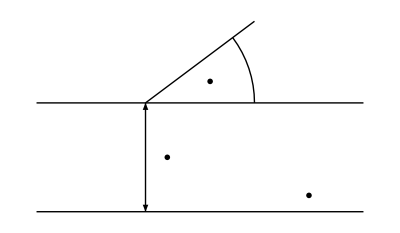

```mathematica
ClearAll[o, e1, e2, ang]
o = {0,0};
e1 = {1, 0};
e2 = {0, 1};
ang[r_] := ArcTan[r//First, r//Last] // N;


ClearAll[modernOpticsLecture1Fig1, a, rth]
a = {4, 3}/4;
th = ang[a];
rth = RotationTransform[th/2] ;
modernOpticsLecture1Fig1 = Graphics[{
Thick,
Line[{o, 3 e1}],
Line[{e2, e2 + 3 e1}],
Line[{e1+e2, e1 + e2 + a }],
Arrowheads[{-.05,.05}],
Arrow[{e1, e1 + e2}],
Text[MaTeX["y_i"], 1.2 e1 + e2/2],
Text[MaTeX["\\alpha_i"], e1 + e2 + rth[{5/4,0}]/2 ],
Circle[ e1 + e2, 1, {0, th}],
Text[MaTeX["\\mbox{optical axis}"], 2.5e1 + 0.15 e2]
}]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture1Fig1", modernOpticsLecture1Fig1]
```

{modernOpticsLecture1Fig1.eps,modernOpticsLecture1Fig1pn.png}

```mathematica
https : // mathematica . stackexchange . com/a/18079/10
```

```mathematica
ClearAll[braceLabel]
braceLabel[{p1_,p2_},lbl_,scale_:.02]:={Arrowheads[{{scale,0,{Graphics@Circle[{1,-1},1,{Pi/2,Pi}],-1}},{scale,1,{Graphics[{Circle[{-1,1},1,{-Pi/2,0}],Inset[lbl,{0,2}]}],1}}}],Arrow[{p1,(p1+p2)/2}],Arrowheads[{{scale,0,{Graphics@Circle[{1,1},1,{Pi,3 Pi/2}],-1}},{scale,1,{Graphics@Circle[{-1,-1},1,{0,Pi/2}],1}}}],Arrow[{(p1+p2)/2,p2}]}
```

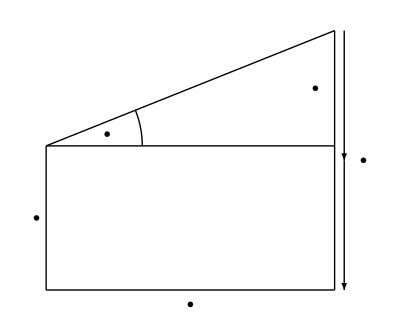

```mathematica
ClearAll[modernOpticsLecture1Fig2, y, l, deltaY, a]
y = 1.5 e2;
l = 3 e1;
deltaY = 1.2 e2;
a = l + deltaY;
th = ang[a];
rth = RotationTransform[-th/2] ;
modernOpticsLecture1Fig2 = Graphics[{
Thick,
Line[{o, l}],
Line[{o, y}],
Line[{y, y + l }],
Line[{l, l + y + deltaY }],
Line[{y, y + a}],
(*braceLabel[{o - 0.1 e1,y - 0.1 e1},""],*)
braceLabel[{l + 0.1 e1 + y + deltaY, l + 0.1 e1},""],
Text[MaTeX["y"], y/2 - 0.1 e1],
Text[MaTeX["L"], l/2 - 0.15 e2],
Text[MaTeX["y'"], l + (y + deltaY)/2 + 0.3 e1],
Text[MaTeX["\\Delta y"], l + y + deltaY/2 - 0.2 e1],
Circle[ y, 1, {0, th}],
Text[MaTeX["\\alpha"], y + rth[a]/5 ]
}]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture1Fig2", modernOpticsLecture1Fig2]
```

{modernOpticsLecture1Fig2.eps,modernOpticsLecture1Fig2pn.png}

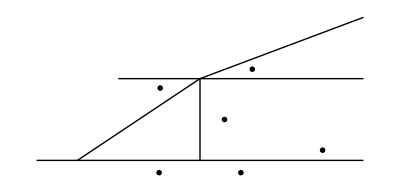

```mathematica
ClearAll[y1, y2, th1, th2, l, modernOpticsLecture1Fig3]
y1 = 2 e2;
y2 = 1.5 e2;
l = 4 e1;
th1 = ang[l + y1];
th2 = ang[l + y2];

modernOpticsLecture1Fig3 = Graphics[{
Thick,
Line[{o, 2 l}],
Line[{l, l + y1}],
Line[{e1,  y1 + l }],
Line[{2 e1 + y1, 2 e1 + y1 + 2 l -2 e1 }],
Line[{y1 +l, y1 + 2 l + y2}],
Text[MaTeX["n"], l - e1 - 0.3 e2 ],
Text[MaTeX["n'"], l + e1 - 0.3 e2 ],
Text[MaTeX["y = y'"], l + y1/2 + 0.6 e1],
Text[MaTeX["\\mbox{optical axis}"], 2 l -  e1 + 0.25 e2],
Text[MaTeX["\\alpha"], l + y1 + RotationTransform[th1/2][-e1] ],
Text[MaTeX["\\alpha'"], l + y1 + 1.3 RotationTransform[th2/2][e1] ]
}]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture1Fig3", modernOpticsLecture1Fig3]
```

{modernOpticsLecture1Fig3.eps,modernOpticsLecture1Fig3pn.png}

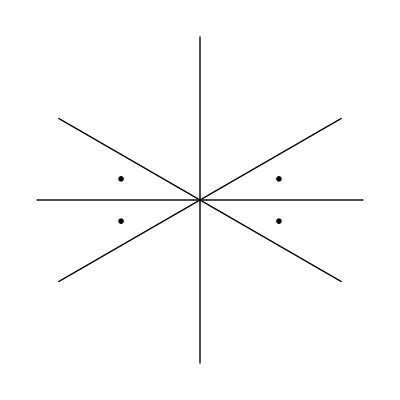

```mathematica
ClearAll[th, a, b, modernOpticsLecture1Fig6]
r[t_] := {Cos[t], Sin[t]}
th = Pi/6;
a = r[th];
b =r[-th];

modernOpticsLecture1Fig6 = Graphics[{
Thick,
Line[{-e1, e1}],
Line[{-e2, e2}],
Line[{-a, a }],
Line[{-b, b }],
Text[MaTeX["+"], r[th/2]/2 ],
Text[MaTeX["-"], r[-th/2]/2 ],
Text[MaTeX["+"], r[Pi - th/2]/2 ],
Text[MaTeX["-"], r[-Pi + th/2]/2 ]
}]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture1Fig6", modernOpticsLecture1Fig6]
```

{modernOpticsLecture1Fig6.eps,modernOpticsLecture1Fig6pn.png}

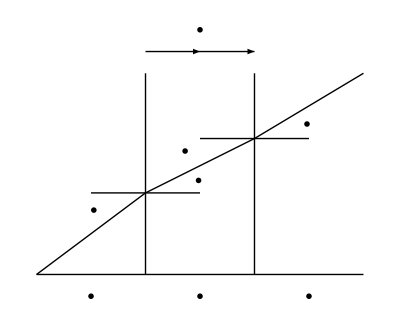

```mathematica
ClearAll[y1, y2, y3, th1, th2, th3, p1, p2, p3, l, dy, modernOpticsLecture1Fig9]
y1 = 0.75 e2;
y2 = 0.5  e2;
y3 = 0.6  e2;
l = e1;
th1 = ang[l + y1];
th2 = ang[l + y2];
th3 = ang[l + y3];
p1 = l + y1;
p2 = p1 + l + y2;
p3 = p2 + l + y3;
dy = y1 + y2 + y3;

modernOpticsLecture1Fig9 = Graphics[{
Thick,
Line[{o, 3 l}],
Line[{o, p1}],
Line[{p1,  p2 }],
Line[{p2, p3 }],
Line[{l, l + dy }],
Line[{2l,2 l + dy }],
Line[{p1 - e1/2, p1 + e1/2 }],
Line[{p2 - e1/2, p2 + e1/2 }],
Text[MaTeX["n"], l/2 - 0.2 e2 ],
Text[MaTeX["n_t"], 1.5 l - 0.2 e2 ],
Text[MaTeX["n'"], 2.5 l - 0.2 e2 ],
Text[MaTeX["\\alpha_0"], l + y1 + RotationTransform[th1/2][-e1]/2 ],
Text[MaTeX["\\alpha_1"], l + y1 + RotationTransform[th2/2][e1]/2 ],
Text[MaTeX["\\alpha_2 = \\alpha_1"], 2 l + y1 + y2 + RotationTransform[th2/2][-e1]/2 - 0.15 e1 ],
Text[MaTeX["\\alpha_3"], 2l + y1 + y2 + RotationTransform[th3/2][e1]/2 ],
braceLabel[{l + dy + 0.2 e2, 2l + dy+ 0.2 e2 },""],
Text[MaTeX["t"], 1.5 l + dy + 0.4 e2],
}]
```

```mathematica
peeters`exportForLatex["modernOpticsLecture1Fig9", modernOpticsLecture1Fig9]
```

{modernOpticsLecture1Fig9.eps,modernOpticsLecture1Fig9pn.png}